```mathematica
N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
Map[FromDigits,Partition[RealDigits@N[π,100],2,1]]
```

{785398163397448309615660845819875721049292349843776455243736148076954101571552249657008706335529267/250000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}

```mathematica
Partition[RealDigits@N[π,100],2,1]
```

{{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,8},1}}

```mathematica
First@Partition[RealDigits@N[π,100],2,1]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,8},1}

```mathematica
MantissaExponent@N[π,100]
```

{0.3141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068,1}

```mathematica
First@Partition[RealDigits@N[π,100],2,1]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,8},1}

```mathematica
Map[FromDigits,Partition[First@RealDigits@N[π,100],2,1]]
```

{31,14,41,15,59,92,26,65,53,35,58,89,97,79,93,32,23,38,84,46,62,26,64,43,33,38,83,32,27,79,95,50,2,28,88,84,41,19,97,71,16,69,93,39,99,93,37,75,51,10,5,58,82,20,9,97,74,49,94,44,45,59,92,23,30,7,78,81,16,64,40,6,62,28,86,62,20,8,89,99,98,86,62,28,80,3,34,48,82,25,53,34,42,21,11,17,70,6,68}

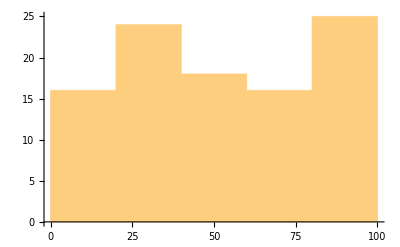

```mathematica
Histogram[Map[FromDigits,Partition[First@RealDigits@N[π,100],2,1]]]
```

```mathematica
Histogram[Map[FromDigits,Partition[First@RealDigits@N[π,1000],2,1]],PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",ImageSize->Full,AspectRatio->1/3]
```

-Graphics-

```mathematica
Histogram[Map[FromDigits,Partition[First@RealDigits@N[π,10000],2,1]],PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",ImageSize->Full,AspectRatio->1/3]
```

-Graphics-

```mathematica
Histogram[Map[FromDigits,Partition[First@RealDigits@N[22/7,10000],2,1]],PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",ImageSize->Full,AspectRatio->1/3]
```

-Graphics-